```mathematica
[-Graphics-](https://mipt.ru/education/chair/theoretical_mechanics/courses/haos-i-kotiki.php)[-Graphics-](https://t.me/miptdesign)-Graphics-mailto: efimov.ss@phystech.eduNonemailto: efimov.ss@phystech.eduHyperlinkHyperlinkActive
```

```mathematica
FastNorm[v_]:=√(Plus@@(v^2)); (*более быстрый вариант стандартной функции Norm[], вычисляющей норму вектора v*)
width=640;height=360;fov=40.°/width; (*параметры изображения: ширина и высота кадра в пикселях, fov - горизонтальный размер поля зрения)*)
```

# 1. Основа Рейтрейсинга

```mathematica
(*Функция трассировки луча. Для заданного луча с началом p0 и направляющим вектором n возвращает цвет точки поверхности ближайшего объекта, на которую попадает луч*)
TraceRay[p0_,n_]:=Module[{col=0 (*цвет фона (черный)*),a,
c0={0,0,0},r0=1}, (*положение центра и радиус сферы (единственного объекта в кадре на данном этапе)*)

a=FastNorm[(c0-p0)×n]; (*прицельный параметр луча относительно центра сферы*)
If[a<r0,col=0.5]; (*при наличии пересечения со сферой цвет меняется на цвет сферы (серый)*)

col
]; 

data=ParallelTable[TraceRay[{0,0,10} (*положение камеры*),#/FastNorm[#]&@{Tan[compx fov],Tan[compy fov],-1.} (*нормированный направляющий вектор луча, идущего через пиксель с координатами {xcomp, ycomp}*)],{compy,height/2,-height/2,-1},{compx,-width/2,width/2}]; (*таблица из цветов всех пикселей кадра*)
Image[data] (*формирование изображения из таблицы*)
```

-Graphics-

```mathematica
(*добавление второй сферы, расположенной позади первой*)
TraceRay[p0_,n_]:=Module[{col=0 ,a,
c0={0,0,0},r0=1,
c1={1,1,-3},r1=1},(*параметры второй сферы*) 

a=FastNorm[(c0-p0)×n]; 
If[a<r0,col=0.5];

(*проверка пересечения со второй сферой*)
a=FastNorm[(c1-p0)×n]; 
If[a<r1,col=0.9 (*светло-серый цвет*)];

col
]; 

data=ParallelTable[TraceRay[{0,0,10} ,#/FastNorm[#]&@{Tan[compx fov],Tan[compy fov],-1.} ],{compy,height/2,-height/2,-1},{compx,-width/2,width/2}]; 
Image[data]
```

-Graphics-

# 2. Учет расстояния до точек объектов

```mathematica
TraceRay[p0_,n_]:=Module[{col=0,d,dist(*расстояние до ближайшего объекта вдоль луча*)=∞(*исходное значение (=расстояние до фона)*),a,
c0={0,0,0},r0=1,
c1={1,1,-3},r1=1},

a=FastNorm[(c0-p0)×n];
If[a<r0,
d=(c0-p0).n+√(r0^2-a^2){-1,1}; (*расстояния от начала луча до двух точек пересечения со сферой*)
If[dist>#,(*проверка на то, что точка находится ближе к началу, чем ранее найденные пересечения (ближе фона при отсутствии таковых)*)
col=0.5;dist=#(*обновление расстояния до ближайшего объекта*)]&/@d;
];

(*вторая сфера (теперь на загораживает впереди стоящую сферу)*)
a=FastNorm[(c1-p0)×n];
If[a<r1,
d=(c1-p0).n+√(r1^2-a^2){-1,1};
If[dist>#,
col=0.9;dist=#]&/@d;
];

col
];

data=ParallelTable[TraceRay[{0,0,10},#/FastNorm[#]&@{Tan[compx fov],Tan[compy fov],-1.}],{compy,height/2,-height/2,-1},{compx,-width/2,width/2}];
Image[data]
```

-Graphics-

# 3. Тени

```mathematica
Clear[TraceRay];(*очистка предыдущей функции для переопределения с необязательным аргументом*)
TraceRay[p0_,n_,sd_:True(*необязательный аргумент, определяющий необходимость вычисления цвета*)]:=Module[{col=0,dist=∞,d,a,p,δ=0.001,(*константа для условий на малые величины*)
c0={0,0,0},r0=1,
l1={1,0,0}(*направление на источник света*)},

a=FastNorm[(c0-p0)×n];
If[a<r0,
d=(c0-p0).n+√(r0^2-a^2){-1,1}; 
If[dist>#>δ,(*исключение самопересечений (необходимо для лучей, запускаемых с поверхности сферы)*)
col=Which[!sd,0 (*случай sd=False (предотвращает лишние рекурентные вызовы функции)*),
p=p0+n #(*координаты точки поверхности*);TraceRay[p,l1,False]⟦2⟧==∞(*проверка на наличие посторонних объектов между точкой и источником света (TraceRay[]⟦2⟧=dist==∞ ⇒ нет пересечений с другими объектами ⇒ точка не в тени)*),0.5, (*цвет в случае нахождения точки на свету*)
True,0](*цвет в случае нахождения точки в тени (черный)*);
dist=#
]&/@d;
];

{col,dist}(*возврат расстояния до точки поверхности вдобавок к цвету*)
];

data=ParallelTable[TraceRay[{0,0,10},#/FastNorm[#]&@{Tan[compx fov],Tan[compy fov],-1.}]⟦1⟧(*выбор из пары {col,dist} первого числа (цвета) для построения изображения*),{compy,height/2,-height/2,-1},{compx,-width/2,width/2}];
Image[data]
```

-Graphics-

# 4. Затенение по Ламберту

```mathematica
Clear[TraceRay];
TraceRay[p0_,n_,sd_:True]:=Module[{col=0,dist=∞,d,a,p,δ=0.001,
c0={0,0,0},r0=1,
l1={1,0,0}},

a=FastNorm[(c0-p0)×n];
If[a<r0,
d=(c0-p0).n+√(r0^2-a^2){-1,1}; 
If[dist>#>δ,
col=Which[!sd,0,p=p0+n #;TraceRay[p,l1,False]⟦2⟧==∞,0.5 (l1.(p-c0))/FastNorm[p-c0](*косинус угла между нормалью поверхности сферы и направлением на источник света (["Затенение по Ламберту"](https://en.wikipedia.org/wiki/Lambertian_reflectance))*),True,0];
dist=#
]&/@d;
];

{col,dist}
];

data=ParallelTable[TraceRay[{0,0,10},#/FastNorm[#]&@{Tan[compx fov],Tan[compy fov],-1.}]⟦1⟧,{compy,height/2,-height/2,-1},{compx,-width/2,width/2}];
Image[data]
```

-Graphics-

# 5. Добавление объекта (сфера)

```mathematica
Clear[TraceRay];
TraceRay[p0_,n_,sd_:True]:=Module[{col=0,dist=∞,d,a,p,h,δ=0.001,
c0={0,0,0},r0=1,
c1={2,1.5,0},r1=0.2,(*возвращение второй сферы*)
l1={1,0,0}},

a=FastNorm[(c0-p0)×n];
If[a<r0,
d=(c0-p0).n+√(r0^2-a^2){-1,1}; 
If[dist>#>δ,
col=Which[!sd,0,p=p0+n #;TraceRay[p,l1,False]⟦2⟧==∞,0.5 (l1.(p-c0))/FastNorm[p-c0],True,0];
dist=#
]&/@d;
];

(*дублироване условия для проверки пересечения со второй сферой*)
a=FastNorm[(c1-p0)×n];
If[a<r1,
d=(c1-p0).n+√(r1^2-a^2){-1,1};
If[dist>#>δ,
col=Which[!sd,0,p=p0+n #;TraceRay[p,l1,False]⟦2⟧==∞,0.8 (l1.(p-c1))/FastNorm[p-c1],True,0];
dist=#
]&/@d;
];

{col,dist}
];

data=ParallelTable[TraceRay[{0,0,10},#/FastNorm[#]&@{Tan[compx fov],Tan[compy fov],-1.}]⟦1⟧,{compy,height/2,-height/2,-1},{compx,-width/2,width/2}];
Image[data]
```

-Graphics-

# 6. Добавление объекта (кольца)

```mathematica
Clear[TraceRay];
TraceRay[p0_,n_,sd_:True]:=Module[{col=0,dist=∞,d,a,p,h,δ=0.001,
c0={0,0,0},r0=1,
c1={2,1.5,0},r1=0.2,
c2={0,0,0},r2=1.5,R2=2.2,n2={0,0,1},(*параметры колец (центр,внутринний/внешний радиусы,нормаль к плоскости)*)
l1={1,0,0}},

a=FastNorm[(c0-p0)×n];
If[a<r0,
d=(c0-p0).n+√(r0^2-a^2){-1,1}; 
If[dist>#>δ,
col=Which[!sd,0,p=p0+n #;TraceRay[p,l1,False]⟦2⟧==∞,0.5 (l1.(p-c0))/FastNorm[p-c0],True,0];
dist=#
]&/@d;
];

a=FastNorm[(c1-p0)×n];
If[a<r1,
d=(c1-p0).n+√(r1^2-a^2){-1,1};
If[dist>#>δ,
col=Which[!sd,0,p=p0+n #;TraceRay[p,l1,False]⟦2⟧==∞,0.8 (l1.(p-c1))/FastNorm[p-c1],True,0];
dist=#
]&/@d;
];

a=n.n2;(*косинус угла падения к клоскости колец*)
If[Abs[a]>δ,(*исключение лучей параллельных плоскости колец*)
d=((c2-p0).n2)/a;p=p0+n d;(*расстояине до точки пересечения с плоскостью и координаты точки пересечения*)
(*аналогично определению цвета точки сферы: *)
If[dist>d>δ&&r2<FastNorm[p-c2]<R2 (*проверка на попадание в интервал между внутренней и внешней границами*),
col=Which[!sd,0,TraceRay[p,l1,False]⟦2⟧==∞,0.25 (*цвет колец (без затенения)*),True,0];
dist=d
];
];

{col,dist}
];

data=ParallelTable[TraceRay[{0,0,10},#/FastNorm[#]&@{Tan[compx fov],Tan[compy fov],-1.}]⟦1⟧,{compy,height/2,-height/2,-1},{compx,-width/2,width/2}];
Image[data]
```

-Graphics-

# 7. Поворот камеры

```mathematica
Clear[TraceRay];
TraceRay[p0_,n_,sd_:True]:=Module[{col=0,dist=∞,d,a,p,h,δ=0.001,
c0={0,0,0},r0=1,
c1={2,1.5,0},r1=0.2,
c2={0,0,0},r2=1.5,R2=2.2,n2={0,0,1},
l1={Cos[3°],0,Sin[3°]}}, (*поворот освещения*)

a=FastNorm[(c0-p0)×n];
If[a<r0,
d=(c0-p0).n+√(r0^2-a^2){-1,1}; 
If[dist>#>δ,
col=Which[!sd,0,p=p0+n #;TraceRay[p,l1,False]⟦2⟧==∞,0.5 (l1.(p-c0))/FastNorm[p-c0],True,0];
dist=#
]&/@d;
];

a=FastNorm[(c1-p0)×n];
If[a<r1,
d=(c1-p0).n+√(r1^2-a^2){-1,1};
If[dist>#>δ,
col=Which[!sd,0,p=p0+n #;TraceRay[p,l1,False]⟦2⟧==∞,0.8 (l1.(p-c1))/FastNorm[p-c1],True,0];
dist=#
]&/@d;
];

a=n.n2;

If[Abs[a]>δ,
d=((c2-p0).n2)/a;p=p0+n d;
If[dist>d>δ&&r2<FastNorm[p-c2]<R2,
col=Which[!sd,0,TraceRay[p,l1,False]⟦2⟧==∞,0.25,True,0];
dist=d
];
];

{col,dist}
];

M=N@RotationMatrix[60°,{0,0,1}].RotationMatrix[60°,{1,0,0}];(*матрица поворота камеры*)
data=ParallelTable[TraceRay[M.(*поворот радиус-вектора камеры*){0,0,10},#/FastNorm[#]&@(M.(*поворот направления камеры*){Tan[compx fov],Tan[compy fov],-1.})]⟦1⟧,{compy,height/2,-height/2,-1},{compx,-width/2,width/2}];
Image[data]
```

-Graphics-

# 8. Генерация текстур

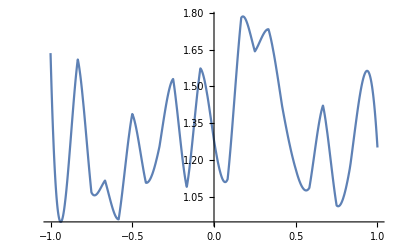

```mathematica
(*задание двух текстурных функций через интерполяцию наборов квази-случайных чисел*)
SeedRandom[1];
tex1=Interpolation[{-1+2.(#-1)/(25-1),.9+.9RandomReal[]}&/@Range[25]];
SeedRandom[5];
tex2=Interpolation[{1+2.(#-1)/(50-1),.6+.6RandomReal[]}&/@Range[50]];
Plot[tex1[x],{x,-1,1}] (*график функции для первой текстуры*)
```

```mathematica
Clear[TraceRay];
TraceRay[p0_,n_,sd_:True]:=Module[{col=0,dist=∞,d,a,p,h,δ=0.001,
c0={0,0,0},r0=1,
c1={2,1.5,0},r1=0.2,
c2={0,0,0},r2=1.5,R2=2.2,n2={0,0,1},
l1={Cos[3°],0,Sin[3°]}},

a=FastNorm[(c0-p0)×n];
If[a<r0,
d=(c0-p0).n+√(r0^2-a^2){-1,1}; 
If[dist>#>δ,
col=Which[!sd,0,p=p0+n #;TraceRay[p,l1,False]⟦2⟧==∞,0.5 (l1.(p-c0))/FastNorm[p-c0] tex1[p⟦3⟧](*модуляция яркости поверхности планеты первой текстурной функцией по координате z*),True,0];
dist=#
]&/@d;
];

a=FastNorm[(c1-p0)×n];
If[a<r1,
d=(c1-p0).n+√(r1^2-a^2){-1,1};
If[dist>#>δ,
col=Which[!sd,0,p=p0+n #;TraceRay[p,l1,False]⟦2⟧==∞,0.8 (l1.(p-c1))/FastNorm[p-c1],True,0];
dist=#
]&/@d;
];

a=n.n2;

If[Abs[a]>δ,
d=((c2-p0).n2)/a;p=p0+n d;
If[dist>d>δ&&r2<FastNorm[p-c2]<R2,
col=Which[!sd,0,TraceRay[p,l1,False]⟦2⟧==∞,0.25tex2[FastNorm[p]](*модуляция яркости колец второй текстурной функцией от расстояния до центра*),True,0];
dist=d
];
];

{col,dist}
];

M=N@RotationMatrix[60°,{0,0,1}].RotationMatrix[60°,{1,0,0}];
data=ParallelTable[TraceRay[M.{0,0,10},#/FastNorm[#]&@(M.{Tan[compx fov],Tan[compy fov],-1.})]⟦1⟧,{compy,height/2,-height/2,-1},{compx,-width/2,width/2}];
Image[data]
```

-Graphics-